```mathematica
Quit[]
```

## SM LO Photon + Z checks

### FeynArts/FormCalc

```mathematica
<<FeynArts`
<<FormCalc`
```

```mathematica
t = CreateTopologies[0, 2 ->2];
diags = InsertFields[t, {F[2,{1}],-F[2,{1}]} -> { F[2,{1}],-F[2,{1}]},ExcludeParticles->{_S}];
Paint[diags,PaintLevel->{Classes},ColumnsXRows->{2,2}];
```

```mathematica
amp = CreateFeynAmp[diags];
res=CalcFeynAmp[amp,FermionChains->VA];
```

```mathematica
_Hel=0;
{Msq, rules}=SquaredME[res,res];
1/2^2*2^4*Msq/.rules/.HelicityME[res,res]/.Den[x_,y_]->1/(x-y)/.ME2->0/.U->-S-T/.T->- S/2 (1-cos);
fcResult=1/(2π)1/(32π S)%//Simplify;
```

### DOI: 10.1016/0550-3213(79)90235-9

```mathematica
ΔLL[x_]:= sw^2 d[x]+gL^2 Δ[x]
ΔLR[x_]:= sw^2 d[x]+gL gR Δ[x]
ΔRL[x_]:=ΔLR[x]
ΔRR[x_]:= sw^2 d[x] +gR^2 Δ[x]
```

```mathematica
d[x_]:= 1/x
Δ[x_]:= 1/(x+MZ2)
```

```mathematica
paperResult=(g^2/(4π))^2  1/(4S)(U^2(ΔLL[-S] + ΔLL[-T])^2+U^2(ΔRR[-S]+ΔRR[-T])^2+2 T^2 ΔRL[-S]^2+2 S^2 ΔRL[-T]^2)/.{gL->a+b,gR->a-b}/.{a->(4 sw^2-1)/(4 cw), b->-1/(4cw)}/.cw->Sqrt[1-sw^2]/.g->Sqrt[4π αEM/sw^2]/.U->-S-T/.T->S(cos-1)/2/.{αEM->Sqrt[Alfa2],sw->Sqrt[SW2]};
```

```mathematica
Limit[paperResult,MZ2->Infinity]/.S->4 energy^2//Simplify
```

```mathematica
fcResult==paperResult//Simplify
```

## NLO photon + LO Z

```mathematica
LOresult = (Alfa2 (2 (-1+cos)^2 (1+cos)^2 S^2 (-4 MZ2+S+cos S)^2 (1-4 SW2)^2+512 (MZ2-S)^2 SW2^2 (2 CW2 (2 MZ2+S-cos S)+S (-1+cos+2 SW2-2 cos SW2))^2+(32 cos CW2 MZ2^2 SW2-4 MZ2 S (-1+cos+6 SW2+4 cos^2 CW2 SW2+cos (-6+4 CW2) SW2-12 SW2^2+12 cos SW2^2)+(-1+cos) S^2 (1+cos+8 cos (-1+2 CW2) SW2+16 cos SW2^2)) (32 cos (3+cos^2) CW2 MZ2^2 SW2-4 MZ2 S (-1+6 SW2+4 cos^4 CW2 SW2-12 SW2^2+cos^2 (1+2 (1+6 CW2) SW2-4 SW2^2)+cos (-1+2 (-1+6 CW2) SW2+4 SW2^2)+cos^3 (1+(-6+4 CW2) SW2+12 SW2^2))+(-1+cos) S^2 (1+3 cos^2+3 cos (1+8 (-1+2 CW2) SW2+16 SW2^2)+cos^3 (1+8 (-1+2 CW2) SW2+16 SW2^2)))+(32 CW2 MZ2^2 SW2+(-1+cos) S^2 (1+cos+8 (-1+2 CW2) SW2+16 SW2^2)-4 MZ2 S (-1+cos+cos (-2+4 CW2) SW2+(2+4 CW2) SW2-4 SW2^2+4 cos SW2^2)) (32 (1+3 cos^2) CW2 MZ2^2 SW2+(-1+cos) S^2 (1+3 cos+cos^3+8 (-1+2 CW2) SW2+16 SW2^2+3 cos^2 (1+8 (-1+2 CW2) SW2+16 SW2^2))-4 MZ2 S (-1+(2+4 CW2) SW2-4 SW2^2+cos (-1+2 (5+2 CW2) SW2-20 SW2^2)+cos^3 (1+2 (-1+6 CW2) SW2+4 SW2^2)+cos^2 (1+2 (-5+6 CW2) SW2+20 SW2^2)))))/(1024 (-1+cos)^2 CW2^2 (MZ2-S)^2 S (2 MZ2+S-cos S)^2 SW2^2);
```

```mathematica
Limit[LOresult,MZ2->Infinity]/.{S-> 4 energy^2,cos->x}//Simplify
```

```mathematica
Alfa2/(4 (-1+x)^2 S)((3+x^2)^2(1+Alfa/π(4(1-u+v-w)Log[(Sqrt[S]/2)/ΔE]+u^2-v^2+w^2+2PolyLog[2,(1+x)/2]-2PolyLog[2,(1-x)/2]-2/3 π^2)) + Alfa/π(1/3 u(3-42x+42 x^2-14 x^3+11 x^4)-v(5-7x+3 x^2-x^3)+1/3 w(111+21x+33 x^2+11 x^3)+1/2 u^2(3+7x-5 x^2-3 x^3-2 x^4)+v^2(3-3x+x^2-x^3)-1/2 w^2(9+7x+11 x^2+5 x^3)-2 u v x (2-x-x^3)-u w (21+3x+9 x^2-3 x^3+2 x^4) + 2 v w(6+5x+4 x^2+x^3) -46/9(9+6 x^2+x^4)+π^2/3(18-15x+12 x^2-3 x^3+4 x^4)))/.{u->Log[S/me^2],v->Log[1/2 S(1+x)/me^2],w->Log[1/2 S(1-x)/me^2]};
%/.{{Alfa->0},{Alfa->1/128,ΔE-> 400*^-3,me-> 0.5*^-6}}/.{Alfa2->1/128^2,S->240^2};
(*Plot[%,{x,-1,1}]*)
%/.x->-0.5
```

## LO Photon + Z + Zprime

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.12 (24 May 2024)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (16 Jan 2023)

by Thomas Hahn

loading generic model file /home/mkirk/Documents/bhabha_bsm/Zprime_FA/Zprime_FA.gen

> $GenericMixing is OFF

generic model {/home/mkirk/Documents/bhabha_bsm/Zprime_FA/Zprime_FA} initialized

loading classes model file /home/mkirk/Documents/bhabha_bsm/Zprime_FA/Zprime_FA.mod

> 44 particles (incl. antiparticles) in 17 classes

> $CounterTerms are ON

> 95 vertices

classes model {/home/mkirk/Documents/bhabha_bsm/Zprime_FA/Zprime_FA} initialized

Excluding 0 Generic, 3 Classes, and 3 Particles fields

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 1 Generic, 3 Classes insertions

> Top. 3: 1 Generic, 3 Classes insertions

> Top. 4: 0 Generic, 0 Classes insertions

Restoring 0 Generic, 3 Classes, and 3 Particles fields

in total: 2 Generic, 6 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

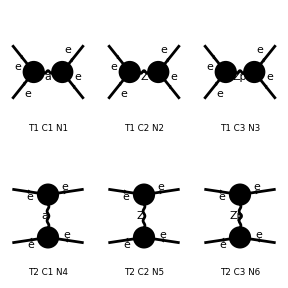

```mathematica
t = CreateTopologies[0, 2 ->2];
diags = InsertFields[t, {F[2,{1}],-F[2,{1}]} -> { F[2,{1}],-F[2,{1}]},ExcludeParticles->{_S},Model->NotebookDirectory[]<>"Zprime_FA/Zprime_FA",GenericModel->NotebookDirectory[]<>"Zprime_FA/Zprime_FA"];
Paint[diags,PaintLevel->{Classes},ColumnsXRows->{3,2}];
```

```mathematica
amp = CreateFeynAmp[diags];
res=CalcFeynAmp[amp,FermionChains->VA];
```

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 3 Classes amplitudes

> Top. 2: 1 Generic, 3 Classes amplitudes

in total: 2 Generic, 6 Classes amplitudes

preparing FORM code in /home/mkirk/Documents/bhabha_bsm/fc-amp-1.frm

running FORM...

ok

```mathematica
_Hel=0;
{Msq, rules}=SquaredME[res,res];
1/2^2*2^4*Msq/.rules/.HelicityME[res,res]/.Den[x_,y_]->1/(x-y)/.Me->0/.U->-S-T/.T->- S/2 (1-cos);
1/(2π)1/(32π S)%/.M$FACouplings/.Conjugate->Identity//Simplify
```

> 36 helicity matrix elements

preparing FORM code in /home/mkirk/Documents/bhabha_bsm/fc-hel-1.frm

running FORM...

ok

1/(64 π^2 S)(((1+cos)^2 S^2 (4 cw^2 (gZprimeL^2-gZprimeR^2) (MZ2-S) (2 MZ2+S-cos S) (-4 MZprime^2+S+cos S) sw^2+Alfa π (MZprime^2-S) (2 MZprime^2+S-cos S) (-4 MZ2+S+cos S) (cw^4-2 cw^2 sw^2-3 sw^4))^2)/(8 cw^4 (MZ2-S)^2 (MZprime^2-S)^2 (2 MZ2+S-cos S)^2 (2 MZprime^2+S-cos S)^2 sw^4)+2 ((8 gZprimeL gZprimeR S)/(2 MZprime^2+S-cos S)-4 Alfa π (2/(-1+cos)+(S (cw^2-sw^2))/(cw^2 (2 MZ2+S-cos S))))^2+S^2 (-(gZprimeL-gZprimeR)^2/(MZprime^2-S)-(4 Alfa π)/(S-cos S)-(2 (gZprimeL^2+gZprimeR^2))/(2 MZprime^2+S-cos S)-(Alfa π (cw^2+sw^2)^2)/(4 cw^2 (MZ2-S) sw^2)-(Alfa π (cw^4-2 cw^2 sw^2+5 sw^4))/(2 cw^2 (2 MZ2+S-cos S) sw^2)) ((1+cos^2) (-(gZprimeL-gZprimeR)^2/(MZprime^2-S)-(4 Alfa π)/(S-cos S)-(2 (gZprimeL^2+gZprimeR^2))/(2 MZprime^2+S-cos S)-(Alfa π (cw^2+sw^2)^2)/(4 cw^2 (MZ2-S) sw^2)-(Alfa π (cw^4-2 cw^2 sw^2+5 sw^4))/(2 cw^2 (2 MZ2+S-cos S) sw^2))-2 cos ((gZprimeL+gZprimeR)^2/(MZprime^2-S)+(4 Alfa cos π)/(S-cos S)+(2 (gZprimeL^2+gZprimeR^2))/(2 MZprime^2+S-cos S)+(Alfa π (cw^2-3 sw^2)^2)/(4 cw^2 (MZ2-S) sw^2)+(Alfa π (cw^4-2 cw^2 sw^2+5 sw^4))/(2 cw^2 (2 MZ2+S-cos S) sw^2)))+S^2 ((gZprimeL+gZprimeR)^2/(MZprime^2-S)+(4 Alfa cos π)/(S-cos S)+(2 (gZprimeL^2+gZprimeR^2))/(2 MZprime^2+S-cos S)+(Alfa π (cw^2-3 sw^2)^2)/(4 cw^2 (MZ2-S) sw^2)+(Alfa π (cw^4-2 cw^2 sw^2+5 sw^4))/(2 cw^2 (2 MZ2+S-cos S) sw^2)) ((1+cos^2) ((gZprimeL+gZprimeR)^2/(MZprime^2-S)+(4 Alfa cos π)/(S-cos S)+(2 (gZprimeL^2+gZprimeR^2))/(2 MZprime^2+S-cos S)+(Alfa π (cw^2-3 sw^2)^2)/(4 cw^2 (MZ2-S) sw^2)+(Alfa π (cw^4-2 cw^2 sw^2+5 sw^4))/(2 cw^2 (2 MZ2+S-cos S) sw^2))+1/2 cos ((4 (gZprimeL-gZprimeR)^2)/(MZprime^2-S)+(16 Alfa π)/(S-cos S)+(8 (gZprimeL^2+gZprimeR^2))/(2 MZprime^2+S-cos S)+(Alfa π (cw^2+sw^2)^2)/(cw^2 (MZ2-S) sw^2)+(2 Alfa π (cw^4-2 cw^2 sw^2+5 sw^4))/(cw^2 (2 MZ2+S-cos S) sw^2))))

## LO Photon + Z + new scalar

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.12 (24 May 2024)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (16 Jan 2023)

by Thomas Hahn

loading generic model file /home/mkirk/Documents/bhabha_bsm/scalar_FA/scalar_FA.gen

> $GenericMixing is OFF

generic model {/home/mkirk/Documents/bhabha_bsm/scalar_FA/scalar_FA} initialized

loading classes model file /home/mkirk/Documents/bhabha_bsm/scalar_FA/scalar_FA.mod

> 44 particles (incl. antiparticles) in 17 classes

> $CounterTerms are ON

> 94 vertices

classes model {/home/mkirk/Documents/bhabha_bsm/scalar_FA/scalar_FA} initialized

Excluding 0 Generic, 2 Classes, and 2 Particles fields

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 2 Generic, 3 Classes insertions

> Top. 3: 2 Generic, 3 Classes insertions

> Top. 4: 0 Generic, 0 Classes insertions

Restoring 0 Generic, 2 Classes, and 2 Particles fields

in total: 4 Generic, 6 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebf/cedf/ef.m, 0 diagrams

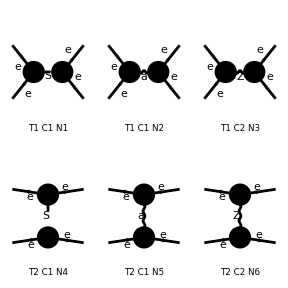

```mathematica
t = CreateTopologies[0, 2 ->2];
diags = InsertFields[t, {F[2,{1}],-F[2,{1}]} -> { F[2,{1}],-F[2,{1}]},ExcludeParticles->{S[1|2]},Model->NotebookDirectory[]<>"scalar_FA/scalar_FA",GenericModel->NotebookDirectory[]<>"scalar_FA/scalar_FA"];
Paint[diags,PaintLevel->{Classes},ColumnsXRows->{3,2}];
```

```mathematica
amp = CreateFeynAmp[diags];
res=CalcFeynAmp[amp,FermionChains->VA];
```

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 2 Generic, 3 Classes amplitudes

> Top. 2: 2 Generic, 3 Classes amplitudes

in total: 4 Generic, 6 Classes amplitudes

preparing FORM code in /home/mkirk/Documents/bhabha_bsm/fc-amp-1.frm

running FORM...

ok

```mathematica
_Hel=0;
{Msq, rules}=SquaredME[res,res];
1/2^2*2^4*Msq/.rules/.HelicityME[res,res]/.Den[x_,y_]->1/(x-y)/.Me->0/.U->-S-T/.T->- S/2 (1-cos);
1/(2π)1/(32π S)%/.M$FACouplings/.Conjugate->Identity//Simplify
```

> 100 helicity matrix elements

preparing FORM code in /home/mkirk/Documents/bhabha_bsm/fc-hel-1.frm

running FORM...

ok

(4 (-1+cos)^2 cos cw^4 gNP^4 (Mscalar^2-S) (MZ2-S)^2 S^2 ((1+cos) Mscalar^2-2 (-1+cos) S) (2 MZ2+S-cos S)^2 sw^4+Alfa2 (-1+cos)^2 (1+cos)^2 π^2 (Mscalar^2-S)^2 S^2 (2 Mscalar^2+S-cos S)^2 (-4 MZ2+S+cos S)^2 (cw^2-3 sw^2) (cw^2+sw^2) (cw^4-2 cw^2 sw^2-3 sw^4)+8 (MZ2-S)^2 sw^4 (1/2 (-1+cos) cw^2 gNP^2 (Mscalar^2-S) S (-2 MZ2+(-1+cos) S)+(-1+cos) cw^2 gNP^2 S (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S)+8 Alfa cw^2 π (Mscalar^2-S) (-2 MZ2+(-1+cos) S) (2 Mscalar^2+S-cos S)+4 Alfa (-1+cos) π (Mscalar^2-S) S (-2 Mscalar^2+(-1+cos) S) (cw^2-sw^2)) (1/2 (-1+cos) cw^2 gNP^2 (Mscalar^2-S) S (-2 MZ2+(-1+cos) S)-1/2 (-1+cos) cos cw^2 gNP^2 (Mscalar^2-S) S (-2 MZ2+(-1+cos) S)+(-1+cos) cw^2 gNP^2 S (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S)+8 Alfa cw^2 π (Mscalar^2-S) (-2 MZ2+(-1+cos) S) (2 Mscalar^2+S-cos S)+4 Alfa (-1+cos) π (Mscalar^2-S) S (-2 Mscalar^2+(-1+cos) S) (cw^2-sw^2))+2 (Mscalar^2-S)^2 (MZ2-S)^2 sw^4 (-((-1+cos) cw^2 gNP^2 S (-2 MZ2+(-1+cos) S))-8 Alfa π (2 Mscalar^2+S-cos S) (cw^2 (4 MZ2+S-cos S)-(-1+cos) S sw^2)) ((-1+cos)^2 cw^2 gNP^2 S (-2 MZ2+(-1+cos) S)-8 Alfa π (2 Mscalar^2+S-cos S) (cw^2 (4 MZ2+S-cos S)-(-1+cos) S sw^2))+8 (Mscalar^2-S)^2 (1/2 (-1+cos) cw^2 gNP^2 (MZ2-S) S (-2 MZ2+(-1+cos) S) sw^2+4 Alfa cw^2 π (MZ2-S) (-2 Mscalar^2+(-1+cos) S) (2 MZ2+S-cos S) sw^2+1/4 Alfa (-1+cos) π S (-2 Mscalar^2+(-1+cos) S) (cw^4 (-4 MZ2+S+cos S)+2 (-3+cos) cw^2 S sw^2+(-12 MZ2+(9+cos) S) sw^4)) ((1+cos^2) (1/2 (-1+cos) cw^2 gNP^2 (MZ2-S) S (-2 MZ2+(-1+cos) S) sw^2+4 Alfa cw^2 π (MZ2-S) (-2 Mscalar^2+(-1+cos) S) (2 MZ2+S-cos S) sw^2+1/4 Alfa (-1+cos) π S (-2 Mscalar^2+(-1+cos) S) (cw^4 (-4 MZ2+S+cos S)+2 (-3+cos) cw^2 S sw^2+(-12 MZ2+(9+cos) S) sw^4))+1/2 cos (-16 Alfa cos cw^2 π (MZ2-S) (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S) sw^2+Alfa (-1+cos) π S (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S) (cw^2-3 sw^2)^2-2 (1-cos) (MZ2-S) S (cw^2 gNP^2 (2 MZ2+S-cos S) sw^2+Alfa π (2 Mscalar^2+S-cos S) (cw^4-2 cw^2 sw^2+5 sw^4))))+8 (Mscalar^2-S)^2 (4 Alfa cos cw^2 π (MZ2-S) (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S) sw^2-1/4 Alfa (-1+cos) π S (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S) (cw^2-3 sw^2)^2+1/2 (1-cos) (MZ2-S) S (cw^2 gNP^2 (2 MZ2+S-cos S) sw^2+Alfa π (2 Mscalar^2+S-cos S) (cw^4-2 cw^2 sw^2+5 sw^4))) (-2 cos (1/2 (-1+cos) cw^2 gNP^2 (MZ2-S) S (-2 MZ2+(-1+cos) S) sw^2+4 Alfa cw^2 π (MZ2-S) (-2 Mscalar^2+(-1+cos) S) (2 MZ2+S-cos S) sw^2+1/4 Alfa (-1+cos) π S (-2 Mscalar^2+(-1+cos) S) (cw^4 (-4 MZ2+S+cos S)+2 (-3+cos) cw^2 S sw^2+(-12 MZ2+(9+cos) S) sw^4))+(1+cos^2) (4 Alfa cos cw^2 π (MZ2-S) (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S) sw^2-1/4 Alfa (-1+cos) π S (-2 Mscalar^2+(-1+cos) S) (-2 MZ2+(-1+cos) S) (cw^2-3 sw^2)^2+1/2 (1-cos) (MZ2-S) S (cw^2 gNP^2 (2 MZ2+S-cos S) sw^2+Alfa π (2 Mscalar^2+S-cos S) (cw^4-2 cw^2 sw^2+5 sw^4)))))/(512 (-1+cos)^2 cw^4 π^2 (Mscalar^2-S)^2 (MZ2-S)^2 S (2 Mscalar^2+S-cos S)^2 (2 MZ2+S-cos S)^2 sw^4)

## LO Photon + Zprime, s channel only

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.12 (24 May 2024)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.10 (16 Jan 2023)

by Thomas Hahn

Excluding 0 Generic, 4 Classes, and 4 Particles fields

inserting at level(s) {Generic,Classes}

> Top. 1: 0 Generic, 0 Classes insertions

> Top. 2: 1 Generic, 2 Classes insertions

> Top. 3: 0 Generic, 0 Classes insertions

> Top. 4: 0 Generic, 0 Classes insertions

Restoring 0 Generic, 4 Classes, and 4 Particles fields

in total: 1 Generic, 2 Classes insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

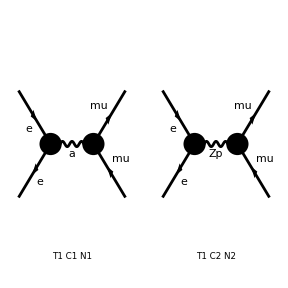

```mathematica
t = CreateTopologies[0, 2 ->2];
diags = InsertFields[t, {F[2,{1}],-F[2,{1}]} -> { F[2,{2}],-F[2,{2}]},ExcludeParticles->{_S,V[2]},Model->NotebookDirectory[]<>"Zprime_FA/Zprime_FA",GenericModel->NotebookDirectory[]<>"Zprime_FA/Zprime_FA"];
Paint[diags,PaintLevel->{Classes},ColumnsXRows->{3,2}];
```

```mathematica
amp = CreateFeynAmp[diags];
res=CalcFeynAmp[amp,FermionChains->VA];
```

creating amplitudes at level(s) {Generic,Classes}

> Top. 1: 1 Generic, 2 Classes amplitudes

in total: 1 Generic, 2 Classes amplitudes

preparing FORM code in /home/mkirk/fc-amp-1.frm

running FORM...

ok

```mathematica
_Hel=0;
{Msq, rules}=SquaredME[res,res];
1/2^2*2^4*Msq/.rules/.HelicityME[res,res]/.Den[x_,y_]->1/(x-y)/.{Me->0,MMU->0}/.U->-S-T/.T->- S/2 (1-cos);
1/(2π)1/(32π S)%/.M$FACouplings/.Conjugate->Identity//Simplify
```

> 16 helicity matrix elements

preparing FORM code in /home/mkirk/fc-hel-1.frm

running FORM...

ok

1/16 ((4 Alfa2 (1+cos^2))/S+1/(π^2 (MZprime^2-S)^2)(-2 Alfa ((1+cos)^2 gZprimeL^2+2 (-1+cos)^2 gZprimeL gZprimeR+(1+cos)^2 gZprimeR^2) π (MZprime^2-S)+((1+cos)^2 gZprimeL^4+2 (-1+cos)^2 gZprimeL^2 gZprimeR^2+(1+cos)^2 gZprimeR^4) S))

```mathematica
Collect[%26,{Alfa2,Alfa},Simplify]
```

-(Alfa ((1+cos)^2 gZprimeL^2+2 (-1+cos)^2 gZprimeL gZprimeR+(1+cos)^2 gZprimeR^2))/(8 π (MZprime^2-S))+(Alfa2 (1+cos^2))/(4 S)+(((1+cos)^2 gZprimeL^4+2 (-1+cos)^2 gZprimeL^2 gZprimeR^2+(1+cos)^2 gZprimeR^4) S)/(16 π^2 (MZprime^2-S)^2)